Autor: Radosław Terelak

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 1

Metoda bisekcji

Napisać procedurę realizującą algorytm metody bisekcji (argumenty:  f, a, b, e).

Korzystając z napisanej procedury:

a) Wyznaczyć wszystkie rzeczywiste pierwiastki wielomianu: f(x)=x^5+4 x^3+2x-8.

b) Wyznaczyć  (z dokładnością 10^-6) najmniejszy dodatni pierwiastek funkcji: h(x)=exp(-x^2) sin x-cos x.

c) Znaleźć (z dokładnością do sześciu cyfr po przecinku) największą liczbę x∈(0,40], dla której jest spełniona nierówność:  10 ln x + 5 ≤  x.

## Rozwiązanie

### Program

```mathematica
bisekcja[f_,a_,b_,e_]:=Module[{ax,bx,m},
m = (a + b) / 2;
ax = a;
bx = b;
While[Abs[f[m]] > e,
If[f[ax]*f[m]<0,bx=m,ax=m];
m=(ax+bx)/2;
];
Return[m]
]
```

### Przykład testowy

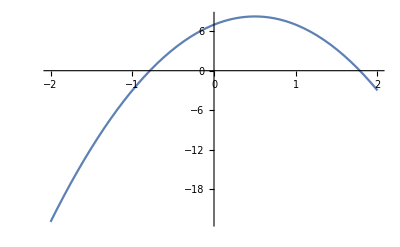

-0.784454

```mathematica
testowy[x_]:=-5 x^2+5x+7
Plot[testowy[x],{x,-2,2}]
bisekcja[testowy,-5,5,0.001] //N
```

### Zadanie a)

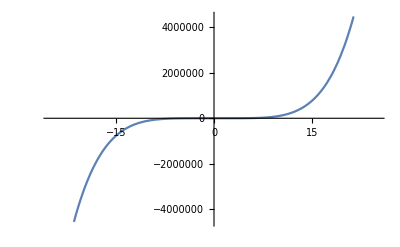

```mathematica
f[x_]:=x^5+4 x^3+2x-8
Plot[f[x],{x,-25,25}]
```

Na wykresie widać, że funkcja ma swoje pierwiastki w zakresie < -10; 10 >

```mathematica
Plot[f'[x],{x,-4000,4000}]
```

-Graphics-

```mathematica
Limit[f'[x],x->-∞]
Limit[f'[x],x->∞]
```

∞

∞

Jak widać funkcja jest monotoniczna. Następnie szukam pierwiastka.

```mathematica
bisekcja[f,-10,10,10^-4]//N
```

1.04968

### Zadanie b)

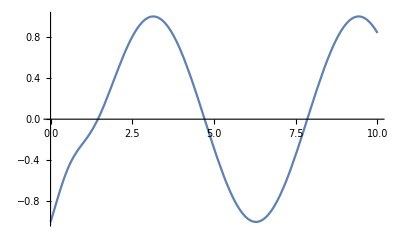

```mathematica
h[x_]:=Exp[-x^2]*Sin[x]-Cos[x]
Plot[h[x],{x,0,10}]
```

Z wykresu widać, że funkcja ma swój najmniejszy dodatni pierwiastek w zakresie < 1; 2 >

```mathematica
bisekcja[h,1,2,10^-6]//N
```

1.44884

### Zadanie c)

10ln(x) + 5 ≤ x
10ln(x) + 5 - x ≤ 0

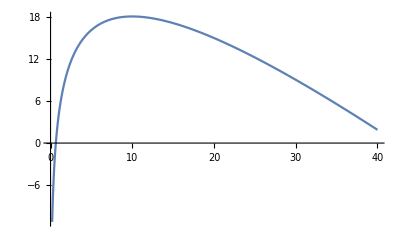

```mathematica
g[x_]:=10Log[x]+5-x
Plot[g[x],{x,0,40}]
```

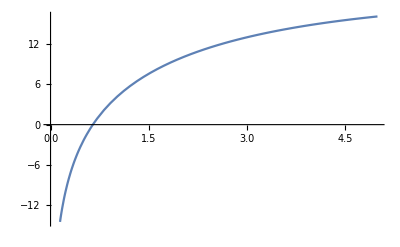

```mathematica
Plot[g[x],{x,0,5}]
```

Po zawężeniu zakresu widać że szukany pierwiastek znajduje się w przedziale < 0; 1 >

```mathematica
bisekcja[g,0,1,10^-6]//N
```

0.647075